```mathematica
(*Зададим основную матрицу системы и столбец свободных членов*)A={{1,1},{1,-1},{2,3}};
B={6,7,8};
(*Найдем количество уравнений в системе уравнений*)
m=Dimensions[A][[1]];
(*Найдем количество переменных в системе уравнений*)
n=Dimensions[A][[2]];
(*Зададим переменные системы уравнений*)
X=Array[x,n];
(*Построим сумму квадратов отклонений левых частей системы уравнений от правых*)
S=Sum[(A[[i]].X-B[[i]])^2,{i,1,m}];
(*Найдем минимум функции S*)
M=NMinimize[S,X];
(*Найдем нормальное псевдорешение системы уравнений*)
PSol=Table[x[j]/.M[[2,j]],{j,1,n}];
Print["Нормальное псевдорешение имеет вид: ",PSol]
```

Нормальное псевдорешение имеет вид: {6.03333,-1.2}

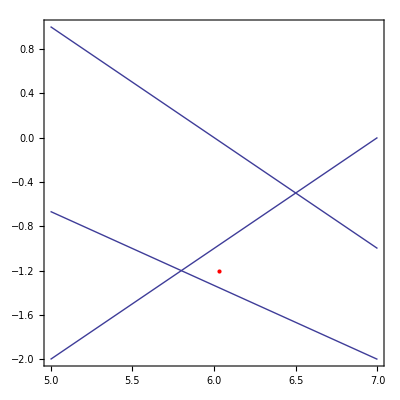

```mathematica
(*Построим графики уравнений системы и её нормальное псевдорешение в одной системе координат*)Eqs=Table[ContourPlot[A[[i]].X==B[[i]],{x[1],5,7},{x[2],-2,2},PlotRange->All],{i,1,m}];
GSol=ListPlot[{PSol},PlotStyle->Red];
Show[Eqs,GSol]
```